```mathematica
(*Parte 1: Condensador de Placas Paralelas*)
```

```mathematica
Equipot[L_,l_,d_,h_,Vo_,τ_,itermax_]:= Module[{i,j,n,k,matriz,iter=0,ϵ=500,temp},
n=Round[L/h];
If[OddQ[n],n,n=n+1];
matriz=Table[0.0,{i,1,n},{j,1,n}];
(*Podemos escoger el potencial cero en los bordes por la misma razon que el potencial tiende a cero cuando la distancia tiende a infinito, y sobre las placas sera una constante porque se le esta aplicando un voltaje*)
For[i=2,i<n,i++,
For[j=2,j<n,j++,
matriz[[i,j]]=0.01;
]
];
While[ ϵ>τ ||iter ≤ itermax ,
ϵ =0;
iter = iter +1;
For[j=2,j<n,j++,
 For[i=2,i<n,i++,
 temp =matriz[[i,j]];
matriz[[ (n+1)/2-Round[l/(2*h)];;(n+1)/2+ Round[l/(2*h)], (n+1)/2-Round[d/(2*h)]]]=Vo/2;matriz[[(n+1)/2-Round[l/(2*h)];; (n+1)/2+Round[l/(2*h)],(n+1)/2+Round[d/(2*h)]]]=-Vo/2;
matriz[[i,j]]=1/4(matriz[[i+1,j]]+matriz[[i-1,j]]+matriz[[i,j+1]]+matriz[[i,j-1]])];
]
];
Return[matriz];
Beep[](*Para saber cuando se acaba*)
];
```

```mathematica
LineasE=Equipot[5*10^-2,2*10^-2,1*10^-2,0.08*10^-2,100,10^-2,500]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0560754,0.112076,0.167893,0.223405,0.278462,0.332883,0.386445,0.438874,0.48984,0.538941,0.585701,0.629565,0.669887,0.705935,0.736893,0.76187,0.779918,0.790056,0.791311,0.782763,0.763602,0.733191,0.691132,0.637329,0.572036,0.495894,0.40994,0.315595,0.21462,0.109056,0.00113851,-0.106793,-0.212401,-0.313448,-0.407893,-0.493975,-0.570273,-0.635747,-0.689756,-0.732042,-0.762701,-0.782125,-0.790949,-0.789977,-0.780124,-0.762358,-0.737653,-0.70695,-0.671134,-0.631015,-0.587319,-0.540684,-0.491662,-0.440724,-0.388266,-0.334619,-0.280052,-0.22479,-0.169014,-0.112875,-0.0564996,0.},{0.,0.11232,0.224495,0.33632,0.447554,0.557907,0.667024,0.774469,0.879703,0.982068,1.08077,1.17487,1.26326,1.34464,1.41756,1.48036,1.53125,1.5683,1.58953,1.59293,1.57661,1.53889,1.47842,1.39436,1.28645,1.15518,1.00181,0.82843,0.637927,0.433886,0.22047,0.00224673,-0.216005,-0.429506,-0.63369,-0.82439,-0.99802,-1.1517,-1.28333,-1.39164,-1.47616,-1.53711,-1.57536,-1.59222,-1.58938,-1.56872,-1.53222,-1.48187,-1.41958,-1.34713,-1.26615,-1.17809,-1.08424,-0.985692,-0.88338,-0.778091,-0.670476,-0.561069,-0.450308,-0.338548,-0.226084,-0.113163,0.},{0.,0.16887,0.337542,0.505722,0.673069,0.839168,1.00351,1.16545,1.32421,1.47883,1.62813,1.77072,1.90493,2.02886,2.14028,2.23671,2.31541,2.37344,2.40771,2.4151,2.39264,2.33763,2.2479,2.122,1.95944,1.76083,1.52806,1.2643,0.973969,0.662615,0.336694,0.00330435,-0.330128,-0.656174,-0.967736,-1.25836,-1.52249,-1.75572,-1.95485,-2.11801,-2.24458,-2.33503,-2.39081,-2.41408,-2.40751,-2.37409,-2.31688,-2.23898,-2.1433,-2.03256,-1.90924,-1.77551,-1.6333,-1.48423,-1.32969,-1.17085,-1.00865,-0.843879,-0.677171,-0.509041,-0.339908,-0.170126,0.},{0.,0.225849,0.451466,0.676493,0.90051,1.123,1.34332,1.56065,1.774,1.98211,2.18347,2.37625,2.55825,2.72694,2.87935,3.01214,3.12158,3.20362,3.25398,3.26829,3.24229,3.17208,3.05444,2.8871,2.66915,2.40123,2.08577,1.72709,1.33127,0.906028,0.460391,0.00429194,-0.451862,-0.897661,-1.32317,-1.71937,-2.07854,-2.39458,-2.66319,-2.88193,-3.05012,-3.16871,-3.23993,-3.26699,-3.25377,-3.20451,-3.12355,-3.01516,-2.88337,-2.73186,-2.56396,-2.3826,-2.19032,-1.98926,-1.78125,-1.56779,-1.35012,-1.12923,-0.905935,-0.680882,-0.454596,-0.22751,0.},{0.,0.283357,0.566474,0.848961,1.13034,1.41004,1.68729,1.96117,2.23046,2.49369,2.74902,2.99422,3.22661,3.44303,3.63978,3.81263,3.95681,4.06709,4.13784,4.16323,4.13749,4.05521,3.91178,3.70382,3.42969,3.08988,2.6873,2.22744,1.71827,1.16999,0.594551,0.00519121,-0.584235,-1.15987,-1.70848,-2.2181,-2.67855,-3.08184,-3.42249,-3.69756,-3.90658,-4.05116,-4.13468,-4.16171,-4.13765,-4.06825,-3.95931,-3.81642,-3.64479,-3.44915,-3.2337,-3.00211,-2.75751,-2.50255,-2.23945,-1.97001,-1.69572,-1.41776,-1.13706,-0.854397,-0.570351,-0.285414,0.},{0.,0.341464,0.682716,1.02336,1.36292,1.70076,2.03609,2.36786,2.69474,3.01504,3.32667,3.62704,3.91303,4.18089,4.4262,4.64385,4.82797,4.97203,5.0689,5.11106,5.09086,5.00099,4.83498,4.5879,4.25694,3.84215,3.34679,2.77762,2.14475,1.46126,0.742638,0.00598525,-0.730743,-1.4496,-2.13346,-2.76686,-3.3367,-3.83288,-4.24864,-4.58069,-4.82901,-4.99636,-5.08767,-5.10938,-5.06879,-4.9735,-4.83101,-4.64841,-4.4322,-4.18819,-3.92147,-3.63643,-3.33676,-3.02557,-2.70542,-2.37837,-2.0461,-1.70993,-1.3709,-1.02982,-0.687321,-0.343907,0.},{0.,0.400207,0.800267,1.19983,1.59843,1.99546,2.39012,2.78131,3.16762,3.54723,3.91784,4.2766,4.61998,4.94373,5.24273,5.51099,5.74153,5.92642,6.05684,6.12326,6.11578,6.02461,5.84083,5.5572,5.16922,4.67596,4.08089,3.3921,2.62224,1.78788,0.90875,0.0066588,-0.895516,-1.7749,-2.60967,-3.38012,-4.06966,-4.66565,-5.15998,-5.54921,-5.83421,-6.0195,-6.1123,-6.1215,-6.05685,-5.92823,-5.74513,-5.51633,-5.24971,-4.9522,-4.62977,-4.28746,-3.92951,-3.5594,-3.17995,-2.79344,-2.40167,-2.00605,-1.60764,-1.20728,-0.805579,-0.403025,0.},{0.,0.45958,0.919122,1.37836,1.8369,2.29421,2.74952,3.20176,3.64951,4.09088,4.52347,4.94423,5.34932,5.73407,6.09276,6.41856,6.70338,6.93783,7.1112,7.21165,7.22649,7.14278,6.94824,6.63241,6.18807,5.6127,4.90959,4.08833,3.16465,2.1595,1.09782,0.00719852,-1.08352,-2.14546,-3.15106,-4.07538,-4.89745,-5.60156,-6.1781,-6.62378,-6.94112,-7.13732,-7.22282,-7.20987,-7.11139,-6.94002,-6.70757,-6.42469,-6.10072,-5.7437,-5.36041,-4.95652,-4.53667,-4.10464,-3.66345,-3.21547,-2.76257,-2.30616,-1.8473,-1.38677,-0.925118,-0.462761,0.},{0.,0.519533,1.03918,1.55881,2.07817,2.59682,3.11412,3.62908,4.14035,4.64607,5.14383,5.63049,6.10206,6.55354,6.97876,7.37013,7.71855,8.01312,8.24116,8.38816,8.43807,8.37392,8.17886,7.83779,7.3394,6.6784,5.85738,4.88769,3.78901,2.58787,1.31585,0.00759328,-1.30076,-2.57307,-3.77467,-4.87403,-5.84457,-6.66664,-7.32888,-7.82871,-8.17139,-8.36823,-8.43431,-8.38645,-8.2416,-8.01574,-7.72334,-7.37705,-6.98768,-6.5643,-6.11443,-5.64419,-5.15852,-4.66137,-4.15584,-3.64431,-3.12862,-2.61009,-2.08971,-1.56815,-1.04584,-0.523062,0.},{0.,0.579965,1.16025,1.7409,2.32184,2.90284,3.48339,4.0627,4.63955,5.21225,5.77847,6.33513,6.87823,7.40266,7.90193,8.36797,8.79075,9.15803,9.45508,9.66448,9.76623,9.73825,9.55754,9.2023,8.65488,7.90539,6.95487,5.81683,4.51631,3.0874,1.5701,0.00783454,-1.55453,-3.07212,-4.50153,-5.80272,-6.94166,-7.89326,-8.64404,-9.19295,-9.54988,-9.73247,-9.7625,-9.66293,-9.45582,-9.16111,-8.79617,-8.37568,-7.91181,-7.41452,-6.89184,-6.35017,-5.79459,-5.22903,-4.65654,-4.0794,-3.49928,-2.91738,-2.33449,-1.75113,-1.16754,-0.58383,0.},{0.,0.640727,1.28202,1.92417,2.56734,3.21151,3.85645,4.50159,5.14599,5.78818,6.42609,7.05687,7.67669,8.28055,8.86197,9.4126,9.92189,10.3765,10.7598,11.0514,11.2268,11.2577,11.1129,10.7609,10.1741,9.33475,8.24096,6.90922,5.37256,3.67556,1.86933,0.00791678,-1.85359,-3.66012,-5.35762,-6.89497,-8.22761,-9.3225,-10.1631,-10.7515,-11.1052,-11.252,-11.2232,-11.0501,-10.7609,-10.3801,-9.92796,-9.42111,-8.87279,-8.2935,-7.69151,-7.07322,-6.4436,-5.8064,-5.16441,-4.5197,-3.87367,-3.22726,-2.58104,-1.93525,-1.28992,-0.644914,0.},{0.,0.701619,1.4041,2.10802,2.81382,3.5218,4.23203,4.94427,5.65793,6.37191,7.08454,7.79336,8.49499,9.18479,9.85664,10.5024,11.1114,11.6697,12.1595,12.5575,12.8348,12.9555,12.8778,12.5562,11.9474,11.02,9.76611,8.20734,6.38968,4.37323,2.22373,0.00783818,-2.20815,-4.35795,-6.37489,-8.19325,-9.7529,-11.0079,-11.9366,-12.5469,-12.8703,-12.9499,-12.8314,-12.5565,-12.161,-11.6739,-11.1181,-10.5117,-9.86839,-9.1988,-8.51097,-7.81098,-7.10337,-6.39149,-5.67772,-4.96371,-4.25052,-3.53871,-2.82853,-2.11991,-1.41257,-0.70611,0.},{0.,0.762389,1.52598,2.29167,3.06026,3.83238,4.60849,5.38876,6.17304,6.96074,7.7507,8.5411,9.3292,10.1111,10.8815,11.6329,12.3554,13.0353,13.6543,14.1877,14.6022,14.8543,14.889,14.6408,14.0409,13.0331,11.5972,9.76519,7.6061,5.20422,2.64452,0.00760139,-2.62941,-5.18942,-7.59179,-9.75155,-11.5845,-13.0214,-14.0305,-14.6319,-14.8818,-14.8491,-14.5991,-14.187,-13.6563,-13.04,-12.3628,-11.643,-10.8941,-10.1261,-9.3463,-8.55992,-7.7708,-6.98162,-6.19415,-5.40948,-4.62819,-3.8504,-3.07592,-2.30433,-1.535,-0.76717,0.},{0.,0.822745,1.64707,2.47423,3.30541,4.14166,4.98386,5.83266,6.68845,7.55123,8.42055,9.29538,10.1739,11.0533,11.9296,12.7966,13.646,14.4657,15.2385,15.9399,16.5349,16.9733,17.1855,17.0792,16.5441,15.4757,13.8256,11.6509,9.06585,6.19329,3.14251,0.00721479,-3.12819,-6.17926,-9.05232,-11.638,-13.8136,-15.4647,-16.5342,-17.0707,-17.1788,-16.9685,-16.5323,-15.9398,-15.241,-14.4709,-13.654,-12.8075,-11.9431,-11.0694,-10.1921,-9.31535,-8.44186,-7.57335,-6.71079,-5.85459,-5.00469,-4.16071,-3.32198,-2.48762,-1.6566,-0.827798,0.},{0.,0.88235,1.76668,2.65466,3.54787,4.4478,5.35584,6.27316,7.20074,8.13931,9.08922,10.0504,11.0222,12.0033,12.9913,13.9823,14.9705,15.9468,16.8978,17.8022,18.6273,19.3213,19.803,19.9483,19.5821,18.5013,16.5796,13.9475,10.8136,7.3608,3.72504,0.00669393,-3.71176,-7.34783,-10.8012,-13.9358,-16.5686,-18.4912,-19.5731,-19.9406,-19.7968,-19.317,-18.6251,-17.8025,-16.9008,-15.9527,-14.9792,-13.9939,-13.0057,-12.0203,-11.0414,-10.0715,-9.11166,-8.16259,-7.22425,-6.29622,-5.37775,-4.46784,-3.56528,-2.66873,-1.7767,-0.88766,0.},{0.,0.94084,1.88409,2.83182,3.78607,4.7488,5.72189,6.70712,7.70611,8.72035,9.75111,10.7994,11.866,12.9511,14.0546,15.1753,16.3111,17.4575,18.6073,19.7472,20.8538,21.8842,22.7591,23.3308,23.3364,22.3689,20.0449,16.7467,12.8808,8.71143,4.39015,0.00606314,-4.37814,-8.69976,-12.8697,-16.7363,-20.0353,-22.3602,-23.3286,-23.324,-22.7537,-21.8805,-20.8522,-19.7481,-18.6109,-17.464,-16.3205,-15.1877,-14.0698,-12.969,-11.8861,-10.8215,-9.77463,-8.74473,-7.73071,-6.73124,-5.74481,-4.76974,-3.80427,-2.84652,-1.89456,-0.946389,0.},{0.,0.997827,1.99849,3.00451,4.01835,5.04248,6.07931,7.13118,8.20044,9.28934,10.4001,11.5349,12.696,13.8855,15.1054,16.358,17.6453,18.9692,20.3306,21.7291,23.1596,24.6055,26.0206,27.2813,28.0652,27.5941,24.4852,20.1141,15.2519,10.2141,5.11804,0.00535666,-5.10746,-10.2039,-15.2423,-20.1053,-24.4774,-27.5872,-28.0588,-27.2756,-26.016,-24.6025,-23.1586,-21.7305,-20.3347,-18.9762,-17.6554,-16.3711,-15.1214,-13.9041,-12.7171,-11.558,-10.4246,-9.31474,-8.22606,-7.1563,-6.10316,-5.06428,-4.03729,-3.0198,-2.00938,-1.0036,0.},{0.,1.05291,2.10909,3.17148,4.24302,5.32664,6.42527,7.54188,8.67945,9.84105,11.0299,12.2492,13.5027,14.7943,16.1285,17.5108,18.9477,20.4474,22.0208,23.6826,25.4531,27.3601,29.4387,31.7103,34.0501,35.458,30.1881,23.973,17.7989,11.7752,5.86255,0.00461772,-5.85346,-11.7665,-17.791,-23.9661,-30.1825,-35.4536,-34.0455,-31.7058,-29.435,-27.3578,-25.4527,-23.6846,-22.0255,-20.455,-18.9583,-17.5245,-16.1452,-14.8137,-13.5246,-12.2731,-11.0553,-9.8674,-8.70601,-7.56791,-6.44998,-5.34921,-4.26264,-3.18732,-2.12036,-1.05888,0.},{0.,1.10568,2.21506,3.33149,4.45834,5.59902,6.75698,7.93573,9.1389,10.3703,11.634,12.9344,14.2763,15.6655,17.1086,18.6139,20.1917,21.8562,23.6266,25.531,27.6131,29.9458,32.6657,36.0724,40.9679,50,36.8365,27.7911,20.1957,13.2252,6.55233,0.00389371,-6.5447,-13.2181,-20.1894,-27.7861,-36.8334,-50,-40.9652,-36.069,-32.6628,-29.9442,-27.6133,-25.5335,-23.6317,-21.8643,-20.2029,-18.6282,-17.126,-15.6857,-14.299,-12.9591,-11.6603,-10.3975,-9.16633,-7.96259,-6.78248,-5.62232,-4.47858,-3.34783,-2.22669,-1.11184,0.},{0.,1.15576,2.31561,3.48331,4.66265,5.85748,7.0717,8.30937,9.57469,10.8721,12.2065,13.5831,15.008,16.488,18.0317,19.6492,21.3539,23.1635,25.1022,27.2053,29.5256,32.1468,35.2079,38.9468,43.7494,50,39.3671,30.1594,21.9677,14.3778,7.1176,0.00322626,-7.11131,-14.372,-21.9627,-30.1556,-39.365,-50,-43.7475,-38.9443,-35.2057,-32.1457,-29.5263,-27.2083,-25.1079,-23.1721,-21.3656,-19.6641,-18.0497,-16.5089,-15.0314,-13.6087,-12.2336,-10.9001,-9.6029,-8.337,-7.09792,-5.88142,-4.68345,-3.5001,-2.32755,-1.16209,0.},{0.,1.20275,2.40997,3.62578,4.85436,6.09994,7.36688,8.65967,9.98303,11.342,12.7419,14.189,15.6898,17.2523,18.886,20.6023,22.416,24.3459,26.4176,28.666,31.1402,33.9103,37.0742,40.7587,45.0831,50,40.4724,31.5118,23.1379,15.2008,7.53699,0.00264078,-7.53186,-15.1961,-23.134,-31.5089,-40.4709,-50,-45.0817,-40.7567,-37.0725,-33.9096,-31.1413,-28.6693,-26.4237,-24.355,-22.4282,-20.6178,-18.9046,-17.2738,-15.7138,-14.2151,-12.7697,-11.3707,-10.0119,-8.68798,-7.39374,-6.12447,-4.87566,-3.64297,-2.4222,-1.20923,0.},{0.,1.24631,2.49743,3.75781,5.03198,6.32453,7.64017,8.98379,10.3605,11.7758,13.2356,14.7463,16.3153,17.9509,19.6629,21.4633,23.3666,25.3911,27.5602,29.9043,32.462,35.2823,38.4216,41.9318,45.8249,50,41.011,32.2773,23.8715,15.7505,7.82686,0.002146,-7.8227,-15.7468,-23.8684,-32.2751,-41.0098,-50,-45.8236,-41.9301,-38.4202,-35.2821,-32.4635,-29.908,-27.5667,-25.4006,-23.3792,-21.4792,-19.682,-17.9729,-16.3399,-14.7731,-13.264,-11.8052,-10.3901,-9.01271,-7.6676,-6.34957,-5.05373,-3.77536,-2.50992,-1.25292,0.},{0.,1.28612,2.57735,3.87844,5.19421,6.52956,7.88951,9.27927,10.7043,12.1703,13.6836,15.2509,16.8796,18.5784,20.3568,22.2264,24.2007,26.2961,28.5321,30.9324,33.5243,36.3378,39.3997,42.723,46.2849,50,41.2942,32.7151,24.3203,16.1029,8.01773,0.00173914,-8.01437,-16.0999,-24.3178,-32.7133,-41.2932,-50,-46.2838,-42.7215,-39.3987,-36.3378,-33.5261,-30.9365,-28.5389,-26.3059,-24.2138,-22.2427,-20.3763,-18.6009,-16.9048,-15.2782,-13.7126,-12.2002,-10.7344,-9.30872,-7.91744,-6.55505,-5.21634,-3.8963,-2.59005,-1.29285,0.},{0.,1.3219,2.64915,3.98679,5.33988,6.71356,8.11313,9.54402,11.0119,12.5228,14.083,15.6995,17.3796,19.1316,20.965,22.89,24.9188,27.0648,29.3437,31.7723,34.3682,37.1471,40.1183,43.2767,46.592,50,41.4506,32.9686,24.5917,16.3231,8.13937,0.00141148,-8.13665,-16.3207,-24.5897,-32.9671,-41.4499,-50,-46.5909,-43.2754,-40.1175,-37.1474,-34.3703,-31.7767,-29.3508,-27.075,-24.9321,-22.9067,-20.9849,-19.1545,-17.4051,-15.7272,-14.1124,-12.5532,-11.0425,-9.57392,-8.14148,-6.73944,-5.36234,-4.00492,-2.66205,-1.32872,0.},{0.,1.35339,2.71235,4.08213,5.468,6.87531,8.30955,9.77633,11.2815,12.8311,14.4317,16.0899,17.8131,19.6092,21.4868,23.4551,25.5243,27.7054,30.0097,32.4485,35.032,37.7665,40.6515,43.6745,46.8066,50,41.5397,33.1168,24.7549,16.4585,8.21519,0.0011523,-8.21296,-16.4565,-24.7533,-33.1157,-41.5391,-50,-46.8057,-43.6733,-40.6508,-37.767,-35.0343,-32.4531,-30.017,-27.7158,-25.538,-23.4721,-21.507,-19.6325,-17.8391,-16.1181,-14.4615,-12.8619,-11.3124,-9.8066,-8.33825,-6.90151,-5.49074,-4.10048,-2.7254,-1.36029,0.},{0.,1.38039,2.76653,4.16384,5.57775,7.0138,8.47759,9.97488,11.5116,13.0939,14.7281,16.4209,18.1794,20.011,21.9233,23.9245,26.023,28.2272,30.5451,32.9837,35.5478,38.2378,41.0482,43.9643,46.9604,50,41.5913,33.2041,24.8527,16.5408,8.2617,0.000951166,-8.25986,-16.5392,-24.8513,-33.2031,-41.5908,-50,-46.9595,-43.9632,-41.0477,-38.2385,-35.5502,-32.9885,-30.5527,-28.2378,-26.0369,-23.9417,-21.9438,-20.0345,-18.2057,-16.4494,-14.7582,-13.1249,-11.5428,-10.0054,-8.50656,-7.04024,-5.60071,-4.18236,-2.7797,-1.38736,0.},{0.,1.40273,2.81135,4.23141,5.66848,7.12821,8.61632,10.1386,11.7011,13.31,14.9714,16.692,18.4784,20.3375,22.2763,24.3018,26.4208,28.6397,30.9639,33.3971,35.9405,38.5912,41.341,44.1751,47.0711,50,41.6214,33.2555,24.9109,16.5903,8.28984,0.000798978,-8.2883,-16.5889,-24.9098,-33.2547,-41.621,-50,-47.0703,-44.1741,-41.3405,-38.5919,-35.9431,-33.4021,-30.9716,-28.6505,-26.4349,-24.3192,-22.297,-20.3612,-18.5048,-16.7207,-15.0017,-13.3413,-11.7326,-10.1694,-8.6455,-7.15484,-5.6916,-4.25006,-2.82461,-1.40975,0.},{0.,1.42027,2.84654,4.28445,5.73968,7.21795,8.72504,10.2669,11.8494,13.4787,15.1611,16.9028,18.7103,20.59,22.5482,24.5909,26.7238,28.9516,31.2778,33.704,36.2289,38.8477,41.5512,44.325,47.1493,50,41.639,33.2856,24.9452,16.6196,8.30657,0.000688334,-8.30524,-16.6184,-24.9442,-33.2849,-41.6386,-50,-47.1485,-44.3241,-41.5509,-38.8486,-36.2315,-33.709,-31.2856,-28.9625,-26.738,-24.6084,-22.569,-20.6139,-18.7369,-16.9317,-15.1916,-13.5102,-11.881,-10.2978,-8.75436,-7.24469,-5.7629,-4.30318,-2.85986,-1.42732,0.},{0.,1.43292,2.8719,4.32267,5.79096,7.28255,8.80327,10.359,11.9559,13.5998,15.297,17.0536,18.8758,20.7696,22.7409,24.795,26.9367,29.1696,31.4959,33.9156,36.4262,39.0219,41.693,44.4254,47.2015,50,41.6489,33.3026,24.9647,16.6363,8.31613,0.000613597,-8.31495,-16.6353,-24.9638,-33.302,-41.6485,-50,-47.2006,-44.4245,-41.6926,-39.0228,-36.429,-33.9207,-31.5037,-29.1806,-26.951,-24.8126,-22.7618,-20.7936,-18.9024,-17.0825,-15.3275,-13.6313,-11.9876,-10.39,-8.83265,-7.30935,-5.81423,-4.34144,-2.88525,-1.43998,0.},{0.,1.44059,2.8873,4.34587,5.82207,7.32172,8.85068,10.4149,12.0203,13.673,15.379,17.1444,18.9753,20.8774,22.8563,24.9169,27.0634,29.2988,31.6245,34.0399,36.5416,39.1232,41.775,44.4833,47.2314,50,41.6539,33.3112,24.9746,16.6449,8.32102,0.000570808,-8.31992,-16.6439,-24.9738,-33.3107,-41.6536,-50,-47.2306,-44.4824,-41.7746,-39.1242,-36.5443,-34.045,-31.6324,-29.3098,-27.0777,-24.9345,-22.8772,-20.9014,-19.0019,-17.1733,-15.4095,-13.7045,-12.052,-10.4459,-8.88005,-7.34852,-5.84533,-4.36463,-2.90064,-1.44766,0.},{0.,1.44326,2.89265,4.35392,5.83286,7.33529,8.86706,10.4341,12.0425,13.6981,15.4071,17.1755,19.0092,20.9141,22.8954,24.9581,27.1061,29.3422,31.6676,34.0813,36.5799,39.1568,41.8021,44.5024,47.2413,50,41.6554,33.3139,24.9776,16.6475,8.32252,0.000557574,-8.32144,-16.6465,-24.9769,-33.3133,-41.6551,-50,-47.2405,-44.5015,-41.8018,-39.1577,-36.5827,-34.0864,-31.6754,-29.3531,-27.1203,-24.9756,-22.9162,-20.9379,-19.0358,-17.2043,-15.4376,-13.7295,-12.0741,-10.465,-8.89635,-7.36201,-5.85606,-4.37263,-2.90596,-1.45031,0.},{0.,1.44091,2.88793,4.34679,5.82327,7.32318,8.85237,10.4168,12.0224,13.6752,15.3813,17.1468,18.9777,20.8798,22.8587,24.9192,27.0656,29.3008,31.6263,34.0415,36.543,39.1244,41.7758,44.4839,47.2317,50,41.6539,33.3112,24.9746,16.6449,8.32102,0.000572983,-8.31992,-16.6439,-24.9738,-33.3107,-41.6536,-50,-47.2309,-44.483,-41.7755,-39.1253,-36.5457,-34.0465,-31.6341,-29.3117,-27.0797,-24.9366,-22.8794,-20.9036,-19.0041,-17.1755,-15.4116,-13.7064,-12.0538,-10.4475,-8.88151,-7.34977,-5.84635,-4.36541,-2.90117,-1.44792,0.},{0.,1.43355,2.87315,4.32451,5.79336,7.28546,8.80665,10.3628,11.96,13.6042,15.3016,17.0584,18.8806,20.7744,22.7456,24.7996,26.941,29.1736,31.4995,33.9188,36.429,39.0242,41.6947,44.4266,47.202,50,41.6489,33.3026,24.9647,16.6363,8.31613,0.000617556,-8.31494,-16.6352,-24.9638,-33.302,-41.6485,-50,-47.2012,-44.4256,-41.6943,-39.0251,-36.4317,-33.9238,-31.5072,-29.1844,-26.955,-24.8169,-22.7661,-20.798,-18.9068,-17.0868,-15.3317,-13.6352,-11.9912,-10.3933,-8.83557,-7.31185,-5.81627,-4.34299,-2.88629,-1.4405,0.},{0.,1.42121,2.8484,4.2872,5.74326,7.22229,8.73009,10.2725,11.8556,13.4853,15.168,16.91,18.7175,20.5972,22.5552,24.5977,26.7302,28.9576,31.2833,33.7088,36.233,38.8511,41.5538,44.3267,47.1502,50,41.639,33.2856,24.9452,16.6196,8.30657,0.000693247,-8.30523,-16.6184,-24.9442,-33.2849,-41.6386,-50,-47.1494,-44.3258,-41.5534,-38.8519,-36.2355,-33.7136,-31.2908,-28.9682,-26.744,-24.6148,-22.5755,-20.6205,-18.7435,-16.9381,-15.1978,-13.516,-11.8864,-10.3027,-8.75873,-7.24843,-5.76594,-4.3055,-2.86142,-1.4281,0.},{0.,1.40397,2.81381,4.23504,5.67322,7.13397,8.623,10.1461,11.7093,13.3187,14.9806,16.7014,18.488,20.347,22.2857,24.3109,26.4294,28.6477,30.9712,33.4036,35.946,38.5957,41.3444,44.1774,47.0723,50,41.6214,33.2555,24.9109,16.5903,8.28985,0.000803486,-8.2883,-16.5889,-24.9098,-33.2547,-41.621,-50,-47.0714,-44.1764,-41.3439,-38.5963,-35.9484,-33.4083,-30.9786,-28.6581,-26.443,-24.3277,-22.3056,-20.37,-18.5135,-16.7292,-15.0099,-13.349,-11.7398,-10.176,-8.65128,-7.15979,-5.69563,-4.25313,-2.82668,-1.41078,0.},{0.,1.38193,2.76959,4.16834,5.58363,7.02094,8.48587,9.98417,11.5217,13.1047,14.7395,16.4327,18.1913,20.0228,21.9349,23.9357,26.0336,28.2371,30.5541,32.9918,35.5546,38.2434,41.0525,43.9672,46.9619,50,41.5913,33.2041,24.8527,16.5408,8.26171,0.000953232,-8.25987,-16.5392,-24.8514,-33.2031,-41.5908,-50,-46.961,-43.9661,-41.0519,-38.244,-35.5569,-32.9962,-30.5613,-28.2472,-26.0469,-23.9522,-21.9545,-20.0453,-18.2165,-16.46,-14.7684,-13.1346,-11.5518,-10.0136,-8.51374,-7.04637,-5.60571,-4.18616,-2.78226,-1.38864,0.},{0.,1.35522,2.71598,4.08748,5.47497,6.88379,8.31939,9.78738,11.2936,12.844,14.4452,16.1038,17.8272,19.6233,21.5006,23.4685,25.537,27.7172,30.0204,32.4581,35.0402,37.7732,40.6566,43.678,46.8084,50,41.5397,33.1168,24.755,16.4585,8.2152,0.001149,-8.21298,-16.4566,-24.7533,-33.1157,-41.5391,-50,-46.8074,-43.6768,-40.6558,-37.7736,-35.0423,-32.4624,-30.0273,-27.727,-25.5499,-23.4846,-21.5198,-19.6454,-17.8519,-16.1306,-14.4736,-12.8734,-11.3231,-9.81626,-8.34678,-6.9088,-5.49668,-4.105,-2.72845,-1.36182,0.},{0.,1.32401,2.65333,3.99295,5.34791,6.72334,8.12447,9.55675,11.0258,12.5377,14.0986,15.7155,17.3959,19.1479,20.981,22.9055,24.9335,27.0786,29.3562,31.7834,34.3777,37.1549,40.1243,43.2807,46.594,50,41.4506,32.9686,24.5918,16.3232,8.13939,0.00139875,-8.13668,-16.3208,-24.5898,-32.9672,-41.4499,-50,-46.593,-43.2794,-40.1234,-37.1551,-34.3795,-31.7874,-29.3628,-27.088,-24.946,-22.9211,-20.9997,-19.1695,-17.42,-15.7418,-14.1264,-12.5664,-11.0547,-9.58505,-8.15132,-6.74784,-5.3692,-4.01013,-2.66556,-1.33048,0.},{0.,1.2885,2.58205,3.88538,5.20326,6.54057,7.90229,9.29362,10.72,12.1871,13.7012,15.269,16.898,18.5967,20.3749,22.2439,24.2174,26.3116,28.5463,30.945,33.5352,36.3467,39.4066,42.7276,46.2872,50,41.2942,32.7152,24.3204,16.103,8.01775,0.00171145,-8.01444,-16.1,-24.318,-32.7134,-41.2933,-50,-46.2861,-42.7262,-39.4054,-36.3466,-33.5367,-30.9487,-28.5525,-26.3207,-24.2295,-22.2591,-20.3931,-18.6178,-16.9215,-15.2946,-13.7283,-12.2151,-10.7482,-9.32127,-7.92853,-6.56452,-5.22407,-3.90217,-2.59401,-1.29483,0.},{0.,1.24894,2.50263,3.76549,5.04199,6.33671,7.65431,8.99967,10.3779,11.7944,13.2551,14.7664,16.3357,17.9713,19.683,21.4827,23.3851,25.4084,27.5761,29.9184,32.4742,35.2924,38.4293,41.937,45.8275,50,41.0111,32.2775,23.8717,15.7507,7.8269,0.002096,-7.82283,-15.747,-23.8686,-32.2753,-41.0099,-50,-45.8263,-41.9353,-38.4279,-35.292,-32.4754,-29.9217,-27.5819,-25.417,-23.3967,-21.4974,-19.7006,-17.9916,-16.3585,-14.7913,-13.2815,-11.8217,-10.4054,-9.02661,-7.67988,-6.36006,-5.06228,-3.78186,-2.51429,-1.25512,0.},{0.,1.20562,2.41563,3.63414,4.86526,6.11321,7.38229,8.67698,10.002,11.3622,12.7632,14.2109,15.7121,17.2746,18.908,20.6237,22.4363,24.365,26.4351,28.6816,31.1538,33.9215,37.0829,40.7647,45.0862,50,40.4726,31.5121,23.1383,15.201,7.53707,0.00255906,-7.53209,-15.1965,-23.1345,-31.5093,-40.4712,-50,-45.0847,-40.7626,-37.0811,-33.9207,-31.1546,-28.6845,-26.4405,-24.3731,-22.4474,-20.6377,-18.925,-17.2943,-15.7342,-14.235,-12.7888,-11.3887,-10.0287,-8.70314,-7.40713,-6.1359,-4.88497,-3.65005,-2.42696,-1.21162,0.},{0.,1.15884,2.3217,3.4923,4.67438,5.87175,7.08829,8.328,9.59508,10.894,12.2294,13.6068,15.0321,16.5122,18.0554,19.6723,21.376,23.1842,25.1213,27.2225,29.5405,32.1593,35.2177,38.9536,43.7529,50,39.3675,30.16,21.9683,14.3782,7.11775,0.00310137,-7.1117,-14.3727,-21.9635,-30.1564,-39.3655,-50,-43.7511,-38.9511,-35.2154,-32.158,-29.5409,-27.2249,-25.1262,-23.1918,-21.3865,-19.6858,-18.0718,-16.5311,-15.0534,-13.6301,-12.2542,-10.9196,-9.62091,-8.35333,-7.11234,-5.89373,-4.69348,-3.50772,-2.33268,-1.16466,0.},{0.,1.10896,2.22154,3.34105,4.47081,5.6142,6.77462,7.95555,9.1606,10.3936,11.6584,12.9596,14.302,15.6913,17.1341,18.6386,20.2154,21.8785,23.6472,25.5496,27.6295,29.9596,32.6767,36.0803,40.9723,50,36.8376,27.7923,20.1967,13.2259,6.55258,0.00371264,-6.54531,-13.2191,-20.1907,-27.7875,-36.8346,-50,-40.9698,-36.0771,-32.6738,-29.9578,-27.6293,-25.5516,-23.6516,-21.8856,-20.2254,-18.6514,-17.1496,-15.7095,-14.3225,-12.982,-11.6823,-10.4183,-9.18552,-7.97998,-6.79783,-5.63541,-4.48925,-3.35594,-2.23214,-1.11458,0.},{0.,1.05636,2.1159,3.18154,4.25614,5.34261,6.44384,7.56276,8.70231,9.86555,11.0556,12.2758,13.5298,14.8215,16.1555,17.5371,18.9729,20.4712,22.0429,23.7027,25.4708,27.3753,29.4511,31.7198,34.0567,35.4618,30.191,23.9752,17.8006,11.7762,5.86295,0.00436719,-5.85436,-11.7681,-17.7931,-23.9687,-30.1857,-35.4576,-34.0522,-31.7154,-29.4474,-27.3729,-25.4701,-23.7041,-22.0468,-20.4777,-18.9822,-17.5492,-16.1703,-14.8389,-13.5494,-12.2973,-11.0785,-9.88927,-8.72625,-7.58623,-6.46615,-5.363,-4.27387,-3.19586,-2.1261,-1.06176,0.},{0.,1.00142,2.00559,3.01498,4.03203,5.05913,6.09867,7.15296,8.22429,9.31491,10.427,11.5628,12.7244,13.914,15.1337,16.3857,17.6719,18.9943,20.3541,21.7505,23.1787,24.6221,26.0345,27.2925,28.0737,27.6003,24.4898,20.1175,15.2544,10.2156,5.11862,0.00502494,-5.10869,-10.206,-15.2454,-20.1093,-24.4824,-27.5938,-28.0676,-27.287,-26.03,-24.619,-23.1774,-21.7514,-20.3574,-19.0003,-17.6806,-16.3971,-15.1478,-13.9305,-12.7431,-11.5833,-10.4489,-9.33758,-8.24719,-7.17543,-6.12002,-5.07866,-4.04901,-3.0287,-2.01536,-1.0066,0.},{0.,0.944545,1.89141,2.84263,3.80018,4.76599,5.74189,6.72962,7.73077,8.7468,9.77896,10.8283,11.8954,12.9808,14.084,15.2041,16.3388,17.4839,18.632,19.7699,20.8742,21.9022,22.7745,23.3436,23.3467,22.3769,20.051,16.7513,12.884,8.71339,4.3909,0.00564175,-4.37972,-8.70253,-12.8737,-16.7416,-20.0421,-22.3687,-23.3393,-23.3371,-22.7692,-21.8985,-20.8724,-19.7703,-18.6348,-17.4893,-16.3468,-15.2148,-14.0972,-12.9964,-11.9132,-10.8477,-9.79975,-8.76838,-7.75257,-6.75102,-5.76224,-4.78461,-3.81637,-2.85572,-1.90073,-0.949487,0.},{0.,0.886138,1.77417,2.66572,3.56231,4.4654,5.3763,6.29619,7.226,8.16642,9.11778,10.08,11.0525,12.0338,13.0216,14.012,14.9992,15.9742,16.9234,17.8259,18.6488,19.3404,19.8196,19.9624,19.5938,18.5107,16.587,13.9531,10.8176,7.36319,3.72596,0.00617864,-3.7137,-7.35121,-10.8061,-13.9422,-16.5768,-18.5013,-19.5854,-19.9552,-19.8137,-19.3362,-18.6465,-17.8258,-16.9257,-15.979,-15.0065,-14.0219,-13.034,-12.0485,-11.0692,-10.0984,-9.13745,-8.18685,-7.24666,-6.31649,-5.39561,-4.48305,-3.57767,-2.67813,-1.78302,-0.89083,0.},{0.,0.826582,1.65466,2.48544,3.32005,4.15949,5.00461,5.85603,6.71408,7.57875,8.44957,9.32549,10.2047,11.0844,11.9605,12.8269,13.6754,14.4938,15.265,15.9646,16.5574,16.9935,17.2033,17.0945,16.5569,15.4862,13.834,11.6573,9.07039,6.19605,3.14358,0.00660608,-3.13045,-6.1832,-9.05798,-11.6454,-13.8229,-15.4761,-16.5478,-17.0866,-17.1969,-16.9888,-16.5546,-15.964,-15.2668,-14.498,-13.6821,-12.8361,-11.972,-11.0982,-10.2204,-9.3428,-8.46808,-7.598,-6.73355,-5.87516,-5.02281,-4.17615,-3.33454,-2.49716,-1.66301,-0.831012,0.},{0.,0.76624,1.5336,2.30292,3.07495,3.85028,4.62933,5.41224,6.1988,6.98841,7.77991,8.57143,9.36024,10.1425,10.9127,11.6636,12.3852,13.0639,13.6814,14.2129,14.6253,14.8753,14.9076,14.657,14.0547,13.0445,11.6064,9.77224,7.61113,5.20729,2.64568,0.00690447,-2.63196,-5.19383,-7.59811,-9.75982,-11.5948,-13.0338,-14.0451,-14.6487,-14.9008,-14.8702,-14.6222,-14.2119,-13.6827,-13.0676,-12.3913,-11.6721,-10.9234,-10.1553,-9.37488,-8.58759,-7.79722,-7.00643,-6.21704,-5.43017,-4.6464,-3.86591,-3.08854,-2.31392,-1.54144,-0.770397,0.},{0.,0.705444,1.41167,2.11919,2.82842,3.5396,4.25275,4.96762,5.68356,6.39947,7.11363,7.8236,8.52596,9.2161,9.88787,10.5332,11.1413,11.6985,12.1868,12.5831,12.8583,12.9769,12.897,12.573,11.9618,11.032,9.77586,8.21488,6.39506,4.37652,2.22497,0.00706274,-2.21093,-4.36274,-6.38172,-8.20214,-9.7639,-11.021,-11.9519,-12.5645,-12.89,-12.9716,-12.8549,-12.5817,-12.1877,-11.7017,-11.1468,-10.5409,-9.89771,-9.22791,-8.53951,-7.83859,-7.12971,-6.41622,-5.70053,-4.9843,-4.26864,-3.55414,-2.84108,-2.12944,-1.41897,-0.709318,0.},{0.,0.644487,1.28946,1.93516,2.58169,3.22901,3.87683,4.52456,5.17122,5.81532,6.45476,7.08668,7.70726,8.31147,8.89285,9.44308,9.9516,10.4051,10.787,11.0769,11.2505,11.2793,11.1323,10.778,10.1888,9.34716,8.25107,6.91705,5.37817,3.67899,1.87061,0.00707666,-1.85654,-3.66518,-5.36479,-6.90428,-8.23907,-9.33612,-10.1789,-10.7694,-11.1252,-11.2739,-11.2469,-11.0753,-10.7875,-10.4078,-9.95644,-9.45004,-8.90182,-8.32229,-7.7197,-7.10048,-6.46957,-5.83076,-5.18687,-4.53997,-3.8915,-3.24245,-2.59339,-1.94462,-1.29621,-0.648068,0.},{0.,0.583616,1.16747,1.75157,2.33579,2.91984,3.5032,4.08503,4.66409,5.23865,5.80637,6.36417,6.90802,7.43282,7.9321,8.39778,8.81985,9.18611,9.48184,9.68966,9.78962,9.75966,9.57683,9.21938,8.66969,7.91791,6.9651,5.82478,4.52202,3.09088,1.57139,0.00694723,-1.55758,-3.07732,-4.50888,-5.81223,-6.95332,-7.90706,-8.65996,-9.21093,-9.56984,-9.75427,-9.78599,-9.68792,-9.48206,-9.18835,-8.82411,-8.404,-7.9402,-7.44264,-6.91935,-6.37675,-5.8199,-5.25276,-4.6784,-4.09912,-3.51662,-2.93214,-2.3465,-1.76023,-1.17365,-0.586895,0.},{0.,0.52303,1.0461,1.56903,2.09153,2.61312,3.13311,3.65049,4.16388,4.67141,5.17063,5.65839,6.13071,6.58257,7.00782,7.39888,7.74665,8.04028,8.26709,8.41261,8.46083,8.39481,8.19774,7.85456,7.35399,6.69077,5.86751,4.89559,3.79467,2.59133,1.31711,0.00667946,-1.30383,-2.57829,-3.78204,-4.88353,-5.85619,-6.68034,-7.34462,-7.84642,-8.19098,-8.38956,-8.45723,-8.41076,-8.26707,-8.04212,-7.75035,-7.4044,-7.01505,-6.59139,-6.1409,-5.66974,-5.18284,-4.68416,-4.17682,-3.66324,-3.14525,-2.62425,-2.10122,-1.57688,-1.0517,-0.526,0.},{0.,0.462879,0.925649,1.388,1.84951,2.30959,2.76744,3.22198,3.67173,4.11482,4.5488,4.97061,5.37643,5.76156,6.1203,6.44583,6.73007,6.96365,7.13589,7.23497,7.24824,7.1628,6.96638,6.64855,6.20215,5.62467,4.9194,4.09599,3.17015,2.16285,1.09903,0.00628149,-1.08655,-2.15059,-3.15827,-4.08465,-4.90875,-5.61486,-6.19333,-6.64088,-6.95998,-7.15781,-7.24477,-7.2331,-7.13569,-6.96514,-6.73326,-6.45066,-6.12669,-5.76937,-5.38548,-4.9807,-4.55967,-4.12618,-3.68327,-3.23335,-2.77829,-2.31953,-1.85816,-1.39501,-0.930649,-0.465533,0.},{0.,0.40326,0.806309,1.20875,1.6101,2.0097,2.40672,2.80003,3.18821,3.56941,3.94132,4.30107,4.64514,4.96925,5.26832,5.53635,5.76638,5.95049,6.07988,6.14506,6.13614,6.04338,5.85786,5.5724,5.18249,4.68726,4.09017,3.39935,2.62744,1.79105,0.90988,0.00576388,-0.898423,-1.7798,-2.61655,-3.38895,-4.0804,-4.67826,-5.17439,-5.56534,-5.85196,-6.03875,-6.13288,-6.14324,-6.07956,-5.95168,-5.76907,-5.54051,-5.27387,-4.97606,-4.65305,-4.30991,-3.95085,-3.57938,-3.19833,-2.81001,-2.41623,-2.01843,-1.6177,-1.21491,-0.8107,-0.405592,0.},{0.,0.344224,0.688177,1.03143,1.37347,1.71363,2.0511,2.38479,2.71337,3.03511,3.34792,3.6492,3.93582,4.20403,4.44942,4.66687,4.85054,4.99392,5.08988,5.13093,5.10944,5.01813,4.85057,4.60182,4.26912,3.85252,3.35533,2.78429,2.14954,1.46417,0.743664,0.00513916,-0.733449,-1.45415,-2.13983,-2.77502,-3.34662,-3.8445,-4.2619,-4.59551,-4.84529,-5.01397,-5.10648,-5.12923,-5.08949,-4.99485,-4.85278,-4.67038,-4.45413,-4.20984,-3.94259,-3.65677,-3.35609,-3.04366,-2.72206,-2.39336,-2.05927,-1.72113,-1.38,-1.03672,-0.691952,-0.346228,0.},{0.,0.285775,0.571259,0.85603,1.13959,1.42132,1.70045,1.97601,2.2468,2.5113,2.76767,3.01367,3.24662,3.46336,3.66018,3.83287,3.97667,4.08636,4.15632,4.18076,4.1539,4.07037,3.92557,3.71615,3.44049,3.09909,2.69488,2.23337,1.72253,1.17256,0.595453,0.0044214,-0.586664,-1.16394,-1.71418,-2.22539,-2.68739,-3.09218,-3.43427,-3.71072,-3.92101,-4.06676,-4.15131,-4.17924,-4.15591,-4.08707,-3.97849,-3.83576,-3.66408,-3.46817,-3.25225,-3.01997,-2.77448,-2.51843,-2.25405,-1.98316,-1.70727,-1.42757,-1.14504,-0.860446,-0.57441,-0.287448,0.},{0.,0.227877,0.455479,0.682423,0.908264,1.13246,1.35435,1.57311,1.78771,1.99689,2.19913,2.39258,2.57506,2.74402,2.8965,3.02916,3.13829,3.21984,3.26955,3.28306,3.25613,3.18488,3.06609,2.89754,2.67829,2.40903,2.0922,1.73211,1.33487,0.90821,0.461147,0.00362591,-0.453939,-0.901136,-1.32802,-1.72557,-2.08606,-2.40337,-2.67319,-2.89308,-3.06234,-3.18191,-3.25399,-3.28179,-3.26917,-3.22036,-3.13971,-3.03144,-2.89959,-2.74786,-2.57955,-2.39761,-2.20457,-2.00259,-1.79351,-1.57883,-1.35981,-1.13747,-0.912628,-0.685957,-0.458001,-0.229216,0.},{0.,0.17046,0.340688,0.510372,0.67915,0.84659,1.01216,1.17522,1.33497,1.49042,1.64042,1.78354,1.91813,2.04227,2.15375,2.25009,2.32856,2.38621,2.41997,2.42674,2.40355,2.34772,2.2571,2.13024,1.96666,1.767,1.53314,1.26827,0.976818,0.664336,0.337286,0.00276892,-0.331782,-0.658934,-0.971586,-1.26328,-1.52845,-1.76267,-1.96276,-2.12683,-2.25423,-2.34544,-2.4019,-2.42574,-2.41965,-2.38657,-2.32959,-2.25178,-2.15605,-2.04513,-1.92149,-1.7873,-1.64449,-1.49469,-1.33931,-1.17951,-1.01625,-0.850342,-0.682421,-0.513021,-0.342579,-0.171464,0.},{0.,0.113425,0.226683,0.339553,0.451781,0.563067,0.673044,0.781265,0.887182,0.990133,1.08932,1.18379,1.27244,1.35398,1.42694,1.48967,1.5404,1.5772,1.59807,1.60104,1.58422,1.54593,1.48484,1.40011,1.29149,1.15948,1.00536,0.831205,0.639918,0.435087,0.220879,0.00186735,-0.217168,-0.431444,-0.636389,-0.827836,-1.00219,-1.15657,-1.28887,-1.39781,-1.4829,-1.54439,-1.5831,-1.60036,-1.59784,-1.57742,-1.54108,-1.49079,-1.42846,-1.35588,-1.27467,-1.18629,-1.09203,-0.992971,-0.89007,-0.784115,-0.675765,-0.565563,-0.453958,-0.341316,-0.227941,-0.114093,0.},{0.,0.0566502,0.113213,0.169574,0.225603,0.281145,0.336013,0.389979,0.442765,0.494035,0.543386,0.590342,0.634343,0.674744,0.710816,0.741742,0.766635,0.784547,0.794504,0.795536,0.786727,0.76727,0.736536,0.694129,0.639958,0.574282,0.497744,0.411387,0.316633,0.215245,0.109268,0.000938544,-0.107402,-0.213414,-0.314859,-0.409694,-0.496154,-0.572815,-0.638636,-0.692972,-0.735561,-0.766493,-0.78616,-0.79519,-0.794385,-0.784656,-0.766969,-0.742295,-0.711574,-0.67569,-0.635452,-0.591587,-0.544735,-0.495449,-0.444204,-0.3914,-0.337369,-0.28239,-0.226689,-0.170453,-0.113841,-0.0569835,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

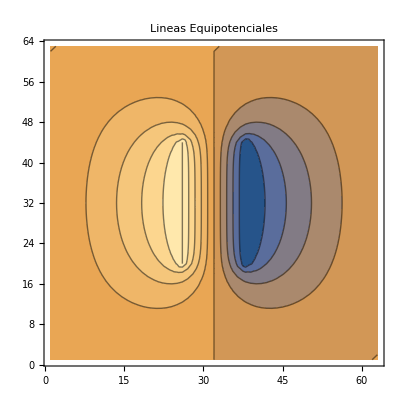

```mathematica
ListContourPlot[LineasE,PlotLabel->HoldForm[Lineas Equipotenciales]]
```

```mathematica
Camp[L_,l_,d_,h_,Vo_,τ_,itermax_,LineasE_]:= Module[{i,j,n,k,matriz,iter=0,ϵ=500,temp,c,x,y,z},
n=Round[L/h];
If[OddQ[n],n,n=n+1];
z={0,0};
c=Table[z,{i,1,n},{j,1,n}];
While[ ϵ>τ ||iter ≤ itermax ,
ϵ =0;
iter = iter +1;
For[j=2,j<n,j++,
 For[i=2,i<n,i++,
c[[i,j]]={1/h (LineasE[[i,j]]-LineasE[[i+1,j]]),1/h (LineasE[[i,j]]-LineasE[[i,j+1]])}];
];
];
Return[c];
Beep[] (*Para saber cuando se acaba*)
];
```

```mathematica
LineasC=Camp[5*10^-2,2*10^-2,1*10^-2,0.08*10^-2,100,10^-2,5,LineasE]
```

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},61,{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},37,{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}}
 |  |  |  |

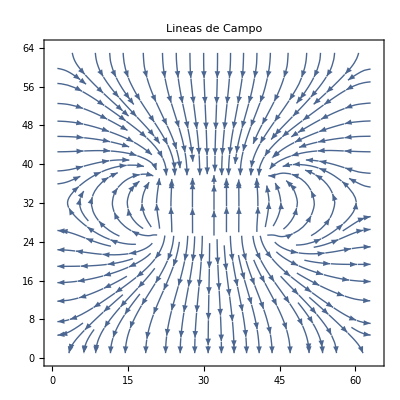

```mathematica
ListStreamPlot[LineasC,PlotLabel->HoldForm[Lineas de Campo],LabelStyle->{FontFamily->"Al Bayan",9,GrayLevel[0]}]
```

```mathematica
Capacit[L_,l_,d_,h_,Vo_, LineasC_]:= Module[{i,n,c,σ=0,epz,Carga,Capacitancia},
epz=8.854187817*10^-12;
n=Round[L/h];
If[OddQ[n],n,n=n+1];
For[i=((n+1)/2-Round[l/(2*h)]),i≤ ((n+1)/2+ Round[l/(2*h)]),i++,
σ=σ+LineasC[[i,(n+1)/2-Round[d/(2*h)]]][[2]]-LineasC[[i,(n+1)/2-Round[d/(2*h)]-1]][[2]];
];
Carga= l*epz*σ;
Capacitancia=Carga/Vo;
Return[Capacitancia];
];
```

```mathematica
Capa=Capacit[5*10^-2,2*10^-2,1*10^-2,0.08*10^-2,100,LineasC]
```

7.28214×10^-10

```mathematica
CapaCero[l_,d_]:=Module[{CapacitanciaCero,epz},
epz=8.854187817*10^-12;
CapacitanciaCero= (epz *l^2)/d;
Return[CapacitanciaCero]
]
```

```mathematica
Ccero=CapaCero[2*10^-2,1*10^-2]
```

3.54168×10^-13

```mathematica
PuntoI3[l_,d_, Capa_,Ccero_]:=Module[{X,Y,z,epz},
Y=Capa/Ccero;
X=d/l;
z={X,Y};
Return[{z}];
];
```

```mathematica
PuntoI3[2*10^-2,1*10^-2,Capa,Ccero]
```

{{1/2,2056.13}}

```mathematica
CCcerodl={{0.5,2056.1284950663794},{0.75,2471.2148277760557},{1,2953.142898175159},{1.25,3547.1373910675393},{1.5,4424.285024744179},{1.75,5757.588674025578},{2,8215.91638033557}}(*~~~Construido Manualmente con d=1,1.5,2,2.5,3,3.5,4~~~*)
```

{{0.5,2056.13},{0.75,2471.21},{1,2953.14},{1.25,3547.14},{1.5,4424.29},{1.75,5757.59},{2,8215.92}}

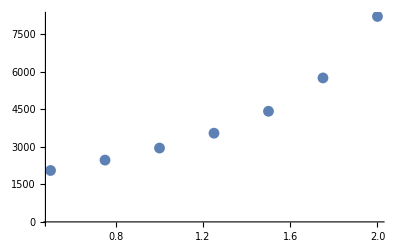

```mathematica
ListPlot[CCcerodl]
```

```mathematica
Show[AxesLabel->{HoldForm[d/l],HoldForm[C/C0]},PlotLabel->None,LabelStyle->{FontFamily->"MS Gothic",10,GrayLevel[0],Bold}]
```

Show::shx: No graphical objects to show.

Show[AxesLabel→{d/l,C/C0},PlotLabel→None,LabelStyle→{FontFamily→MS Gothic,10,-Graphics-,Bold}]

```mathematica
(* Parte 2: Placas Angulares*)
```

```mathematica
V1[x_,y_,V0_,α_]:=V0/α ArcTan[y/x];
E1={-1/(√(x^2+y^2))D[V1[x,y,V0,α], x],-1/(√(x^2+y^2))D[V1[x,y,V0,α], y]}//FullSimplify
```

{(V0 y)/((x^2+y^2)^(3/2) α),-(V0 x)/((x^2+y^2)^(3/2) α)}

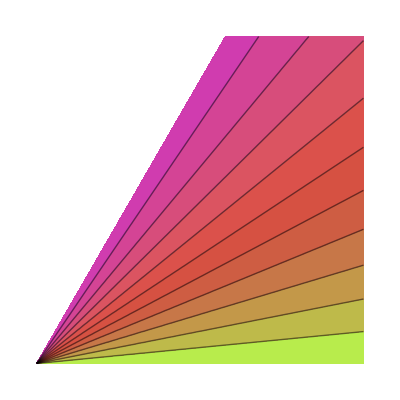

```mathematica
PlotV1=ContourPlot[V1[x,y,1,π/3],{x,0.001,5},{y,0.001,5},Contours->15,RegionFunction->Function[{x,y,z},ArcTan[y/x]≤π/3],Frame->False,ColorFunction->"NeonColors",AspectRatio->Automatic]
```

```mathematica
PlotE1=StreamPlot[E1/.{α->π/3,V0->1},{x,0.001,5},{y,0.001,5},StreamStyle->Blue,RegionFunction->Function[{x,y},ArcTan[y/x]≤π/3],Frame->False,AspectRatio->Automatic];
```

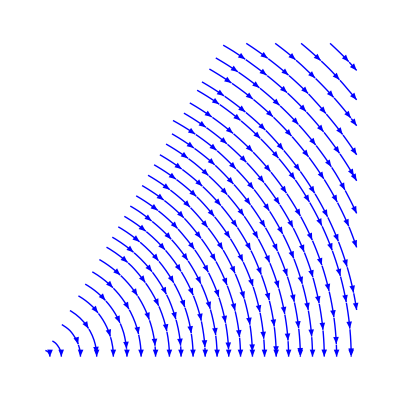

```mathematica
Show[PlotE1]
```

```mathematica
(*Parte 3: Cilindro Separado*)
```

```mathematica
V2in[r_,ϕ_,V0_,a_,M_]:=2V0 ∑_(m=1)^M (r/a)^(2m-1)Sin[(2m-1) ϕ]/((2m-1) π);
V2out[r_,ϕ_,V0_,a_,M_]:=2V0 ∑_(m=1)^M (a/r)^(2m-1)Sin[(2m-1) ϕ]/((2m-1) π);
```

```mathematica
PlotV2in=ContourPlot[V2in[r,ϕ,1,1,100]/.{r->Norm[{x,y}],ϕ->ArcTan[x,y]},{x,-2,2},{y,-2,2},Contours->25,RegionFunction->(Sqrt[#1^2+#2^2]<1&),ColorFunction->"NeonColors",Frame->False];
PlotV2out=ContourPlot[V2out[r,ϕ,1,1,100]/.{r->Norm[{x,y}],ϕ->ArcTan[x,y]},{x,-2,2},{y,-2,2},Contours->25,RegionFunction->(Sqrt[#1^2+#2^2]>1&),Frame->False];
```

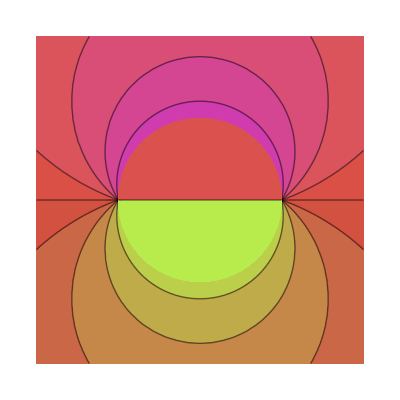

```mathematica
Show[PlotV2out,PlotV2in]
```

```mathematica
(*Parte 4: cilindro completo*)
```

```mathematica
jzero[i_]:=BesselJZero[0,i]//N;
V3[r_,ϕ_,z_,V0_,a_,M_]:=8V0∑_(i=1)^M N[BesselJ[2,jzero[i]]/(jzero[i]^2 BesselJ[1,jzero[i]]^2 Sinh[2jzero[i]])]BesselJ[0,jzero[i] r/a]Sinh[jzero[i] z/a];
```

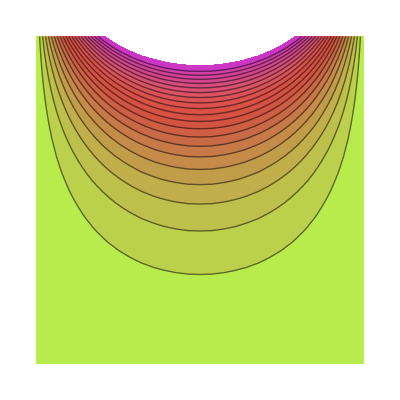

```mathematica
PlotV3long=ContourPlot[V3[x,0,y,1,1,2],{x,-1,1},{y,0,2},Contours->20,ColorFunction->"NeonColors",Frame->False,AspectRatio->Automatic]
```

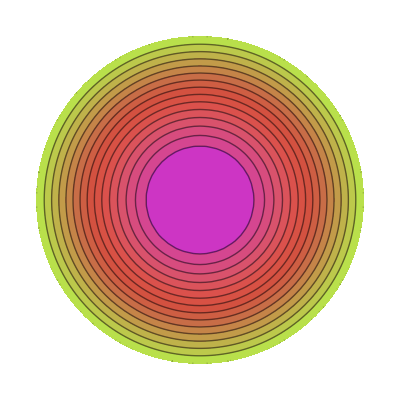

```mathematica
PlotV3trans=ContourPlot[V3[r,ϕ,1,1,1,2]/.{r->Norm[{x,y}],ϕ->ArcTan[x,y]},{x,-1,1},{y,-1,1},Contours->20,ColorFunction->"NeonColors",RegionFunction->(Sqrt[#1^2+#2^2]<1&),Frame->False]
```

```mathematica
(*Parte 5: Cascaron esferico con densidad de carga*)
```

```mathematica
V4in[x_,y_,z_]:=-y;
V4out[x_,y_,z_]:=-y/((x^2+y^2+z^2)^(3/2));
```

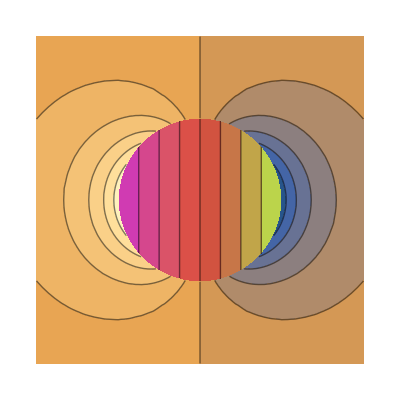

```mathematica
PlotV4in1=ContourPlot[V4in[0,x,y],{x,-2,2},{y,-2,2},Contours->15,RegionFunction->Function[{x,y,z},√(x^2+y^2)≤1],Frame->False,ColorFunction->"NeonColors",AspectRatio->Automatic];
PlotV4out1=ContourPlot[V4out[0,x,y],{x,-2,2},{y,-2,2},Contours->15,RegionFunction->Function[{x,y,z},√(x^2+y^2)≥1],Frame->False,AspectRatio->Automatic];
Show[PlotV4in1,PlotV4out1]
```

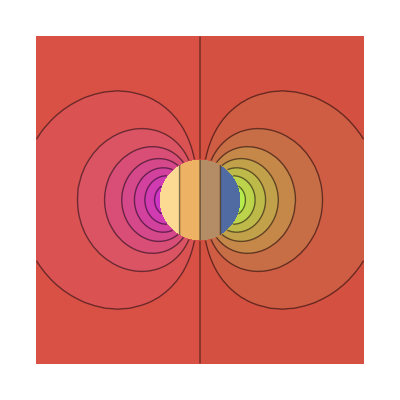

```mathematica
PlotV4in2=ContourPlot[V4in[0.5,x,y],{x,-2,2},{y,-2,2},Contours->15,RegionFunction->Function[{x,y,z},√(x^2+y^2)≤0.5],Frame->False,AspectRatio->Automatic];
PlotV4out2=ContourPlot[V4out[0.5,x,y],{x,-2,2},{y,-2,2},Contours->15,RegionFunction->Function[{x,y,z},√(x^2+y^2)≥0.5],Frame->False,ColorFunction->"NeonColors",AspectRatio->Automatic];
Show[PlotV4in2,PlotV4out2]
```